```mathematica
Id = IdentityMatrix[2];
(*switching mirror convention to nothing on transmission and a sign change on one face of a mirror and nothing on the other, let the reflection matrix off the side which recieves a -1 sign change be called aR*)
{R1, aR1, T1, R2,aR2,T2, RBS, aRBS, TBS} = {r1 Id, -r1 Id, t1 Id, Id,-Id,0 Id, 1/2^(1/2)Id, -1/2^(1/2)Id,1/2^(1/2)Id };
(*rotation*)
P[ϕ_]:=({{Cos[ϕ], -Sin[ϕ]}, {Sin[ϕ], Cos[ϕ]}})
(*propagation across a space of length D = L + δl*)
SpacePropa[L_,δl_]:=Exp[ⅈ Ω/c(L+δl)]P[(Subscript[ω, 0] δl)/c]
(*squeezer*)
SSqz[r_,ϕ_]:=({{Cos[2 ϕ]Sinh[r]+Cosh[r], Sin[2 ϕ]Sinh[r]}, {Sin[2 ϕ]Sinh[r], -Cos[2 ϕ]Sinh[r]+Cosh[r]}})
(*input field quadratures in frequency domain, caret/hat (^) means frequency dependant*)
{nvec, avec, Avec} = {{{Subscript[n̂, 1]}, {Subscript[n̂, 2]}},{{Subscript[â, 1]}, {Subscript[â, 2]}},{{A Cos[Subscript[θ, 0]]}, {A Sin[Subscript[θ, 0]]}}};
```

```mathematica
(*squeezing midway through the cavity*)
cavP = FullSimplify[SpacePropa[L/2,δl/2].SSqz[r,ϕ].SpacePropa[L/2,δl/2]];
(*NB: should alter the set-up s.t. the beam is only squeezed from one direction, i.e. from M1 to M2 but not back from M2 to M1.*)
(*calculating the cavity reflection matrix by borrowing the empty cavity solution and substituting in the above propagation matrix
Subscript[a, 5]=(Subscript[R, 1]+Subscript[T, 1](Id-P Subscript[R, 2] P Subscript[R, 1])^-1 P Subscript[R, 2] P Subscript[T, 1])Subscript[a, 0]
simplifying result using that (δl Ω)/c << 1*)
cavMatrix = FullSimplify[(aR1+T1.Inverse[Id - cavP.R2.cavP.R1].cavP.R2.cavP.T1)/.{(δl Subscript[ω, 0])/c-> ψ,((L+δl) Ω)/c->(L Ω)/c}];
(*the field reflected off the cavity*)
areflvec = FullSimplify[cavMatrix.nvec];
```

```mathematica
(*frequency domain quadratures at the photodiodes*)
aPD1vec = Simplify[TBS.(Avec+avec)+RBS.areflvec];
aPD2vec = Simplify[aRBS.(Avec+avec)+TBS.areflvec];
```

(*homodyne readout takes the difference between the two photo-currents,each of which is proportional to the time average of the intensity of the field,due to the slow response of the PD's*)
i_hom=i_1-i_2
(*let tilde/squiggle (~) mean time-domain*)
i_1∝⟨Ĩ[t]⟩=⟨(|OverHat[Ẽ]_PD1[t]|)^2⟩
OverHat[Ẽ]_PD1[t] =C_0( OverHat[ã]_(PD1,c)[t]Cos[ω_0 t]+OverHat[ã]_(PD1,s)[t]Sin[ω_0 t])
OverHat[ã]_(PD1,c)[t] = InverseFourierTransform[(â)_(PD1,c)[Ω],Ω,t]

(*time-domain intensity of the light at photo-diode 1*)
⟨(Ĩ)_PD1[t]⟩ = C_0^2⟨(|OverHat[ã]_(PD1,c)[t]Cos[ω_0 t]+OverHat[ã]_(PD1,s)[t]Sin[ω_0 t]|)^2⟩

(*assume time domain quadratures are Hermitian*)
⟨(Ĩ)_PD1[t]⟩ = C_0^2⟨(OverHat[ã]_(PD1,c)[t])^2 Cos[ω_0 t]^2+(OverHat[ã]_(PD1,s)[t])^2 Sin[ω_0 t]^2+
(OverHat[ã]_(PD1,c)[t]OverHat[ã]_(PD1,s)[t]+OverHat[ã]_(PD1,s)[t]OverHat[ã]_(PD1,c)[t])Sin[ω_0 t]Cos[ω_0 t]⟩

(*time average of Sin[ω_0 t]Cos[ω_0 t] is zero, time average of Cos[ω_0 t]^2 or Sin[ω_0 t]^2 is 1/2.
then assume quadratures change slowly wrt ω_0*)
⟨(Ĩ)_PD1[t]⟩ =C_0^2/2((OverHat[ã]_(PD1,c)[t])^2+(OverHat[ã]_(PD1,s)[t])^2)

(*spliting time signals into average and time varying parts*)
OverHat[ã]_(PD1,c)[t] = B_(1,c)+OverHat[b̃]_(1,c)[t]
OverHat[ã]_(PD1,s)[t] = B_(1,s)+OverHat[b̃]_(1,s)[t]
⟨(Ĩ)_PD1[t]⟩ =C_0^2/2((B_(1,c)+OverHat[b̃]_(1,c)[t])^2+(B_(1,s)+OverHat[b̃]_(1,s)[t])^2)
⟨(Ĩ)_PD1[t]⟩ =C_0^2/2((B_(1,c))^2+(B_(1,s))^2+(OverHat[b̃]_(1,s)[t])^2+(OverHat[b̃]_(1,c)[t])^2+2(B_(1,c)OverHat[b̃]_(1,c)[t]+B_(1,s)OverHat[b̃]_(1,s)[t]))

(*assume time varying part is small wrt average s.t. time varying part squared is vanishingly small
this is true for comparing quantum noise to the local oscillator*)
⟨(Ĩ)_PD1[t]⟩ =C_0^2/2((B_(1,c))^2+(B_(1,s))^2+2(B_(1,c)OverHat[b̃]_(1,c)[t]+B_(1,s)OverHat[b̃]_(1,s)[t]))

(*apply Fourier transform*)
I_PD1[Ω] =C_0^2/2(((B_(1,c))^2+(B_(1,s))^2)δ[Ω-0]+2(B_(1,c)(b̂)_(1,c)[Ω]+B_(1,s)(b̂)_(1,s)[Ω]))

(*but we are only interested in the quantum noise, not the DC part*)
I_PD1[Ω] =C_0^2(B_(1,c)(b̂)_(1,c)[Ω]+B_(1,s)(b̂)_(1,s)[Ω])

(*homodyne readout is proportional to the difference in intensities, since the Fourier transform is linear we can look at the difference in the spectra*)
I_hom[Ω]=⟨I_PD1[Ω]-I_PD2[Ω]⟩
I_hom[Ω]=C_0^2(B_(1,c)(b̂)_(1,c)[Ω]+B_(1,s)(b̂)_(1,s)[Ω]-B_(2,c)(b̂)_(2,c)[Ω]-B_(2,s)(b̂)_(2,s)[Ω])

(*identify these components as the constant and frequency dependant parts of the original quadratures*)
aPD1vec = ((â)_(PD1,c)[Ω]
(â)_(PD1,s)[Ω]) = (B_(1,c)
B_(1,s)) +((b̂)_(1,c)[Ω]
(b̂)_(1,s)[Ω]) 
aPD2vec=((â)_(PD2,c)[Ω]
(â)_(PD2,s)[Ω]) = (B_(2,c)
B_(2,s)) +((b̂)_(2,c)[Ω]
(b̂)_(2,s)[Ω]) 
(*NB: this doesn't sound true, the added constant picks up a delta function when transformed forwards or backwards?*)

```mathematica
(*spotting the frequency dependent sections by eye*)
Column[{aPD1vec[[1]],aPD1vec[[2]],aPD2vec[[1]],aPD2vec[[2]]}]
```

{1/(√2)(A Cos[θ_0]+(â)_1+(-r1 (n̂)_1-ⅇ^((4 ⅈ L Ω)/c) r1 (r1^2+t1^2) (n̂)_1+ⅇ^((2 ⅈ L Ω)/c) (((2 r1^2+t1^2) (Cos[2 ψ] Cosh[r]^2+Sinh[r]^2)+t1^2 Cos[2 ϕ] Cos[ψ] Sinh[2 r]) (n̂)_1+2 t1^2 Cos[ψ] Cosh[r] (-Cosh[r] Sin[ψ]+Sin[2 ϕ] Sinh[r]) (n̂)_2))/(1+ⅇ^((4 ⅈ L Ω)/c) r1^2-2 ⅇ^((2 ⅈ L Ω)/c) r1 (Cos[2 ψ] Cosh[r]^2+Sinh[r]^2)))}
{1/(√2)(A Sin[θ_0]+(â)_2+(-r1 (n̂)_2+ⅇ^((2 ⅈ L Ω)/c) (t1^2 (Cosh[r]^2 Sin[2 ψ]+Cos[ψ] Sin[2 ϕ] Sinh[2 r]) (n̂)_1+(-ⅇ^((2 ⅈ L Ω)/c) r1 (r1^2+t1^2)+(2 r1^2+t1^2) (Cos[2 ψ] Cosh[r]^2+Sinh[r]^2)-t1^2 Cos[2 ϕ] Cos[ψ] Sinh[2 r]) (n̂)_2))/(1+ⅇ^((4 ⅈ L Ω)/c) r1^2-2 ⅇ^((2 ⅈ L Ω)/c) r1 (Cos[2 ψ] Cosh[r]^2+Sinh[r]^2)))}
{1/(√2)(-A Cos[θ_0]-(â)_1+(-r1 (n̂)_1-ⅇ^((4 ⅈ L Ω)/c) r1 (r1^2+t1^2) (n̂)_1+ⅇ^((2 ⅈ L Ω)/c) (((2 r1^2+t1^2) (Cos[2 ψ] Cosh[r]^2+Sinh[r]^2)+t1^2 Cos[2 ϕ] Cos[ψ] Sinh[2 r]) (n̂)_1+2 t1^2 Cos[ψ] Cosh[r] (-Cosh[r] Sin[ψ]+Sin[2 ϕ] Sinh[r]) (n̂)_2))/(1+ⅇ^((4 ⅈ L Ω)/c) r1^2-2 ⅇ^((2 ⅈ L Ω)/c) r1 (Cos[2 ψ] Cosh[r]^2+Sinh[r]^2)))}
{1/(√2)(-A Sin[θ_0]-(â)_2+(-r1 (n̂)_2+ⅇ^((2 ⅈ L Ω)/c) (t1^2 (Cosh[r]^2 Sin[2 ψ]+Cos[ψ] Sin[2 ϕ] Sinh[2 r]) (n̂)_1+(-ⅇ^((2 ⅈ L Ω)/c) r1 (r1^2+t1^2)+(2 r1^2+t1^2) (Cos[2 ψ] Cosh[r]^2+Sinh[r]^2)-t1^2 Cos[2 ϕ] Cos[ψ] Sinh[2 r]) (n̂)_2))/(1+ⅇ^((4 ⅈ L Ω)/c) r1^2-2 ⅇ^((2 ⅈ L Ω)/c) r1 (Cos[2 ψ] Cosh[r]^2+Sinh[r]^2)))}

```mathematica
(*2^(1/2) expression for freq-dependent avoids using Simplify*)
({{Subscript[B, 1,c], Subscript[b̂, 1,c]}, {Subscript[B, 1,s], Subscript[b̂, 1,s]}, {Subscript[B, 2,c], Subscript[b̂, 2,c]}, {Subscript[B, 2,s], Subscript[b̂, 2,s]}})=1/2^(1/2)({{A Cos[Subscript[θ, 0]], 2^(1/2) aPD1vec[[1]][[1]]-2^(1/2)Subscript[B, 1,c]}, {A Sin[Subscript[θ, 0]], 2^(1/2) aPD1vec[[2]][[1]]-2^(1/2)Subscript[B, 1,s]}, {-A Cos[Subscript[θ, 0]], 2^(1/2) aPD2vec[[1]][[1]]-2^(1/2)Subscript[B, 2,c]}, {-A Sin[Subscript[θ, 0]], 2^(1/2) aPD2vec[[2]][[1]]-2^(1/2)Subscript[B, 2,s]}});
```

```mathematica
(*computing the homodyne intensity (OverHat[HomI][Ω]= OverHat[Subscript[I, hom]][Ω]) in frequency domain
NB: I've dropped Subscript[C, 0] here, should it have stayed it? and if so, what is it?*)
OverHat[HomI]=Simplify[Subscript[B, 1,c] Subscript[b̂, 1,c]+Subscript[B, 1,s] Subscript[b̂, 1,s]-Subscript[B, 2,c] Subscript[b̂, 2,c]-Subscript[B, 2,s] Subscript[b̂, 2,s]]
(*notice that the laser noise (Subscript[â, 1],Subscript[â, 2]) has cancelled out, just as expected for homodyne readout*)
```

-((A ((r1 Cos[θ_0]+ⅇ^((4 ⅈ L Ω)/c) r1^3 Cos[θ_0]+ⅇ^((4 ⅈ L Ω)/c) r1 t1^2 Cos[θ_0]-ⅇ^((2 ⅈ L Ω)/c) Cosh[r]^2 ((2 r1^2+t1^2) Cos[2 ψ] Cos[θ_0]+t1^2 Sin[2 ψ] Sin[θ_0])-ⅇ^((2 ⅈ L Ω)/c) (2 r1^2+t1^2) Cos[θ_0] Sinh[r]^2-ⅇ^((2 ⅈ L Ω)/c) t1^2 Cos[2 ϕ] Cos[ψ] Cos[θ_0] Sinh[2 r]-ⅇ^((2 ⅈ L Ω)/c) t1^2 Cos[ψ] Sin[2 ϕ] Sin[θ_0] Sinh[2 r]) (n̂)_1+(ⅇ^((2 ⅈ L Ω)/c) Cosh[r]^2 (t1^2 Cos[θ_0] Sin[2 ψ]-(2 r1^2+t1^2) Cos[2 ψ] Sin[θ_0])-4 ⅇ^((2 ⅈ L Ω)/c) t1^2 Cos[ϕ] Cos[ψ] Cos[θ_0] Cosh[r] Sin[ϕ] Sinh[r]+Sin[θ_0] (r1+ⅇ^((4 ⅈ L Ω)/c) r1^3+ⅇ^((4 ⅈ L Ω)/c) r1 t1^2-ⅇ^((2 ⅈ L Ω)/c) (2 r1^2+t1^2) Sinh[r]^2+ⅇ^((2 ⅈ L Ω)/c) t1^2 Cos[2 ϕ] Cos[ψ] Sinh[2 r])) (n̂)_2))/(1+ⅇ^((4 ⅈ L Ω)/c) r1^2-2 ⅇ^((2 ⅈ L Ω)/c) r1 Cos[2 ψ] Cosh[r]^2-2 ⅇ^((2 ⅈ L Ω)/c) r1 Sinh[r]^2))

```mathematica
(*extracting the co-efficients of Subscript[n̂, 1], Subscript[n̂, 2]*)
g1[Ω_,r1_,t1_,L_,ψ_,r_,ϕ_,θ_]:=(r1 Cos[θ]+ⅇ^((4 ⅈ L Ω)/c) r1^3 Cos[θ]+ⅇ^((4 ⅈ L Ω)/c) r1 t1^2 Cos[θ]-ⅇ^((2 ⅈ L Ω)/c) Cosh[r]^2 ((2 r1^2+t1^2) Cos[2 ψ] Cos[θ]+t1^2 Sin[2 ψ] Sin[θ])-ⅇ^((2 ⅈ L Ω)/c) (2 r1^2+t1^2) Cos[θ] Sinh[r]^2-ⅇ^((2 ⅈ L Ω)/c) t1^2 Cos[2 ϕ] Cos[ψ] Cos[θ] Sinh[2 r]-ⅇ^((2 ⅈ L Ω)/c) t1^2 Cos[ψ] Sin[2 ϕ] Sin[θ] Sinh[2 r])
g2[Ω_,r1_,t1_,L_,ψ_,r_,ϕ_,θ_]:=(ⅇ^((2 ⅈ L Ω)/c) Cosh[r]^2 (t1^2 Cos[θ] Sin[2 ψ]-(2 r1^2+t1^2) Cos[2 ψ] Sin[θ])-4 ⅇ^((2 ⅈ L Ω)/c) t1^2 Cos[ϕ] Cos[ψ] Cos[θ] Cosh[r] Sin[ϕ] Sinh[r]+Sin[θ] (r1+ⅇ^((4 ⅈ L Ω)/c) r1^3+ⅇ^((4 ⅈ L Ω)/c) r1 t1^2-ⅇ^((2 ⅈ L Ω)/c) (2 r1^2+t1^2) Sinh[r]^2+ⅇ^((2 ⅈ L Ω)/c) t1^2 Cos[2 ϕ] Cos[ψ] Sinh[2 r]))
g3[Ω_,r1_,t1_,L_,ψ_,r_,ϕ_,θ_]:=(1+ⅇ^((4 ⅈ L Ω)/c) r1^2-2 ⅇ^((2 ⅈ L Ω)/c) r1 Cos[2 ψ] Cosh[r]^2-2 ⅇ^((2 ⅈ L Ω)/c) r1 Sinh[r]^2)
```

OverHat[HomI][Ω]= A/g3[Ω;r1,t1,L,ψ,r,ϕ,θ_0](g1[Ω;r1,t1,L,ψ,r,ϕ,θ_0](n̂)_1[Ω] 
+ g2[Ω;r1,t1,L,ψ,r,ϕ,θ_0](n̂)_2[Ω])
OverHat[HomI][Ω]= A/g3[Ω](g1[Ω](n̂)_1[Ω] + g2[Ω](n̂)_2[Ω])

(*computing the power spectral density (PSD) of the homodyne intensity, this quantifies the quantum noise.
Let |0⟩ represent the vacuum (ground) state, for reasons I don't understand, we take expectation against this instead of the actual state.*)
OverHat[S_HomI][Ω] 2π δ[Ω-Ω'] = ⟨0|OverHat[HomI][Ω]○OverHat[HomI]†[Ω']|0⟩

(*[D]pg.35, from assuming the time domain is Hermitian, frequency domain obeys (a_(c,s))^†[Ω] = a_(c,s)[-Ω]*)
(*NB: for now, I'll assume OverHat[HomI][Ω] is Hermitian, although I think that this is wrong*)
OverHat[S_HomI][Ω] 2π δ[Ω-Ω'] = 1/2⟨0|OverHat[HomI][Ω]OverHat[HomI]†[Ω']+OverHat[HomI]†[Ω']OverHat[HomI][Ω]|0⟩
OverHat[S_HomI][Ω] 2π δ[Ω-Ω'] = 1/2⟨0|A/g3[Ω](g1[Ω](n̂)_1[Ω] + g2[Ω](n̂)_2[Ω])A/g3[Ω'](g1[Ω'](n̂)_1[Ω'] + g2[Ω'](n̂)_2[Ω'])+A/g3[Ω'](g1[Ω'](n̂)_1[Ω'] + g2[Ω'](n̂)_2[Ω'])A/g3[Ω](g1[Ω](n̂)_1[Ω] + g2[Ω](n̂)_2[Ω])|0⟩

(*expanding out terms and spotting symmetric products*)
OverHat[S_HomI][Ω] 2π δ[Ω-Ω'] = A^2/(g3[Ω]g3[Ω'])⟨0|g1[Ω]g1[Ω']((n̂)_1[Ω]○(n̂)_1[Ω'])+g2[Ω]g2[Ω']((n̂)_2[Ω]○(n̂)_2[Ω'])
+g1[Ω]g2[Ω']((n̂)_1[Ω]○(n̂)_2[Ω'])+g2[Ω]g1[Ω']((n̂)_2[Ω]○(n̂)_1[Ω'])|0⟩

(*results from the top of [D]pg.38*)
⟨0|(n̂)_1[Ω]○(n̂)_1[Ω']|0⟩ = 1/2 2π δ[Ω-Ω']
⟨0|(n̂)_2[Ω]○(n̂)_2[Ω']|0⟩ = 1/2 2π δ[Ω-Ω']
⟨0|(n̂)_1[Ω]○(n̂)_2[Ω'] |0⟩=⟨0| (n̂)_2[Ω]○(n̂)_1[Ω'] |0⟩= 0

(*as so we have the PSD of the homodyne intensity, to quantify the quantum noise*)
OverHat[S_HomI][Ω] δ[Ω-Ω'] = (A^2(g1[Ω]g1[Ω']+g2[Ω]g2[Ω']))/(2g3[Ω]g3[Ω'])δ[Ω-Ω']
OverHat[S_HomI][Ω] = (A^2(g1[Ω]^2+g2[Ω]^2))/(2 g3[Ω]^2)

```mathematica
setupSHomI = Simplify[(A^2(g1[Ω,r1,t1,L,ψ,r,ϕ,θ]^2+g2[Ω,r1,t1,L,ψ,r,ϕ,θ]^2))/(2 g3[Ω,r1,t1,L,ψ,r,ϕ,θ]^2)]
```

(A^2 ((-r1 Cos[θ]-ⅇ^((4 ⅈ L Ω)/c) r1^3 Cos[θ]-ⅇ^((4 ⅈ L Ω)/c) r1 t1^2 Cos[θ]+ⅇ^((2 ⅈ L Ω)/c) Cosh[r]^2 ((2 r1^2+t1^2) Cos[θ] Cos[2 ψ]+t1^2 Sin[θ] Sin[2 ψ])+ⅇ^((2 ⅈ L Ω)/c) (2 r1^2+t1^2) Cos[θ] Sinh[r]^2+ⅇ^((2 ⅈ L Ω)/c) t1^2 Cos[θ] Cos[2 ϕ] Cos[ψ] Sinh[2 r]+ⅇ^((2 ⅈ L Ω)/c) t1^2 Cos[ψ] Sin[θ] Sin[2 ϕ] Sinh[2 r])^2+(ⅇ^((2 ⅈ L Ω)/c) Cosh[r]^2 ((r1^2+t1^2) Sin[θ-2 ψ]+r1^2 Sin[θ+2 ψ])+ⅇ^((2 ⅈ L Ω)/c) t1^2 Cos[θ] Cos[ψ] Sin[2 ϕ] Sinh[2 r]-Sin[θ] (r1+ⅇ^((4 ⅈ L Ω)/c) r1^3+ⅇ^((4 ⅈ L Ω)/c) r1 t1^2-ⅇ^((2 ⅈ L Ω)/c) (2 r1^2+t1^2) Sinh[r]^2+ⅇ^((2 ⅈ L Ω)/c) t1^2 Cos[2 ϕ] Cos[ψ] Sinh[2 r]))^2))/(2 (1+ⅇ^((4 ⅈ L Ω)/c) r1^2-2 ⅇ^((2 ⅈ L Ω)/c) r1 Cos[2 ψ] Cosh[r]^2-2 ⅇ^((2 ⅈ L Ω)/c) r1 Sinh[r]^2)^2)

```mathematica
(*c = 3 10^8 (*m s^-1*), L in m, Ω in Hz*)
SHomI[inA_,inΩ_,inr1_,int1_,inL_,inψ_,inr_,inϕ_,inθ_] := setupSHomI /.{A->inA,Ω->inΩ,r1->inr1,t1->int1,L->inL,ψ->inψ,r->inr,ϕ->inϕ,θ->inθ,c-> 3 10^8}
```

```mathematica
(*validating SHomI against known plots*)
SetDirectory[NotebookDirectory[]];
```

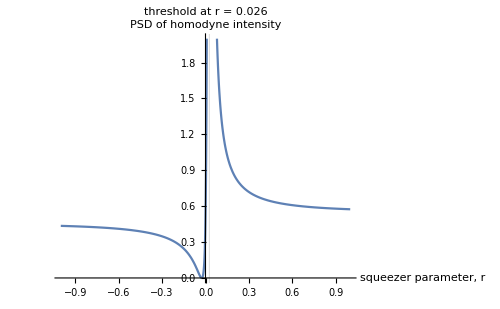

```mathematica
(*PSD vs squeezer parameter r,
L value not important given Ω = 0*)
rThresh = 0.026;
plot = Plot[SHomI[1,0,0.9^(1/2),0.1^(1/2),1,0,r,0,0],{r,-1,1},
AxesLabel->{"squeezer parameter, r","PSD of homodyne intensity"},GridLines->{{rThresh},{}},ImageSize->500, PlotRange->{All,2},PlotLabel->StringForm["threshold at r = ``",rThresh]]
Export["not_main_PSD_vs_r.pdf",plot];
```

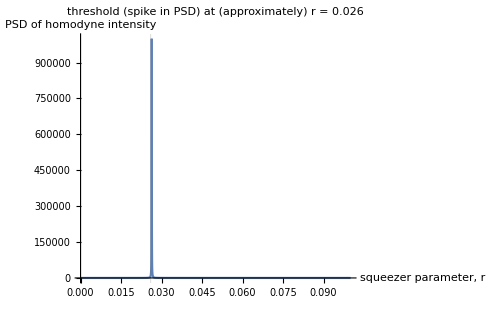

```mathematica
(*PSD vs squeezer parameter r,
zoomed to show threshold spike*)
plot = Plot[SHomI[1,0,0.9^(1/2),0.1^(1/2),1,0,r,0,0],{r,0,0.1},
AxesLabel->{"squeezer parameter, r","PSD of homodyne intensity"},GridLines->{{rThresh},{}},ImageSize->500, PlotRange->{All,10^6},PlotLabel->StringForm["threshold (spike in PSD) at (approximately) r = ``",rThresh]]
Export["not_main_PSD_vs_r_spike.pdf",plot];
```

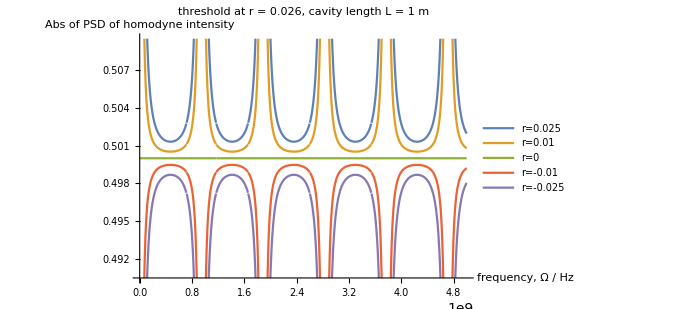

```mathematica
(*PSD vs frequency Ω,
exponents are of the form Exp[ⅈ (L Ω)/c]*)
{rplt1,rplt2,rplt3,rplt4} = {0.025,0.01,-0.01,-0.025};
cavityLength = 1(*m*);
plot = Plot[{Abs[SHomI[1,Ω,0.9^(1/2),0.1^(1/2),cavityLength,0,rplt1,0,0]],Abs[SHomI[1,Ω,0.9^(1/2),0.1^(1/2),cavityLength,0,rplt2,0,0]],Abs[SHomI[1,Ω,0.9^(1/2),0.1^(1/2),cavityLength,0,0,0,0]],Abs[SHomI[1,Ω,0.9^(1/2),0.1^(1/2),cavityLength,0,rplt3,0,0]],
Abs[SHomI[1,Ω,0.9^(1/2),0.1^(1/2),cavityLength,0,rplt4,0,0]]},{Ω,0,5 10^9},
AxesLabel->{"frequency, Ω / Hz","Abs of PSD of homodyne intensity"},PlotLegends->{StringForm["r=``",NumberForm[rplt1,3]],StringForm["r=``",NumberForm[rplt2,3]],"r=0",StringForm["r=``",NumberForm[rplt3,3]],StringForm["r=``",NumberForm[rplt4,3]]},PlotLabel->StringForm["threshold at r = ``, cavity length L = `` m",rThresh,cavityLength],ImageSize->500]
Export["not_main_PSD_vs_freq.pdf",plot];
```

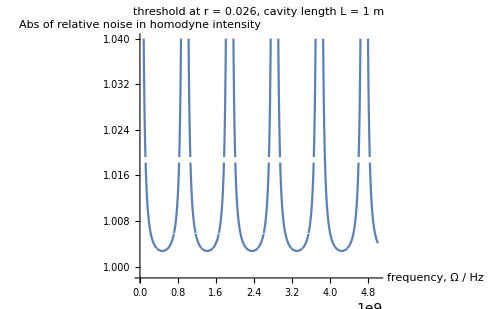

```mathematica
(*relative noise S[r=rThresh]/S[r=0] vs frequency Ω*)
plot = Plot[Abs[SHomI[1,Ω,0.9^(1/2),0.1^(1/2),cavityLength,0,rThresh,0,0]/SHomI[1,Ω,0.9^(1/2),0.1^(1/2),cavityLength,0,0,0,0]],{Ω,0,5 10^9},
AxesLabel->{"frequency, Ω / Hz","Abs of relative noise in homodyne intensity"},PlotLabel->StringForm["threshold at r = ``, cavity length L = `` m",rThresh,cavityLength],PlotRange->{2*0.499,2*0.52},ImageSize->500]
Export["not_main_relative_noise_vs_freq.pdf",plot];
```

```mathematica
(*notebook needs to be saved for this to function*)
NotebookPrint[EvaluationNotebook[],NotebookDirectory[]<>"not_main_notebook.pdf"]
```